Approximation of phi values at ESS for long periods between transfers
for the system without arbitrium signalling + regulation

If the intervals between transfers are sufficiently long, the distribution of strains within the free phage population is a representation of the strain distribution in the lysogen compartment. The strain distribution in the lysogen compartment is determined during the initial phase of the infection, when susceptible cells are still present (S>0). After this phase, the lysogens do grow in numbers but the proportion of strains within this compartment no longer changes because all lysogens grow with the same characteristics. Hence, to optimize the strain frequency in the transmitted phage sample, a strain “should” optimize the number of lysogens formed during the initial phase.

Simplifying assumptions:
- Assume that bacterial dynamics are much slower than phage infection dynamics.
- Assume lysogen growth (due to infections) during the initial phase is small, and hence N = approx S.
- Assume that during the initial phase, S is fixed (S=1) and then drops to 0.
Let T be the duration of the initial phase (for which S>0). [T is a function of ϕ.]
- Assume T is defined as happening when all cells initially present (S=1) have become infected.
Then for the period t = 0 - T, the system is decribed by:
dL / dt = ϕ β P
dP / dt = ((1-ϕ) β - a) P
Hence:
P(t) = P0 Exp[ ((1-ϕ)β - a) t ]
And:
L(t) = ϕ β P0 / ((1-ϕ)β - a)  ( Exp[ ((1-ϕ)β - a) t ] - 1)

Strategy:
(1) Consider ϕ fixed, find T as a function of ϕ.
(2) Consider T to be fixed, find the optimal ϕ given T.
(3) Combine (1) and (2) to find ϕ*.

Standard Parameters:

```mathematica
P0default = 0.01 * (0.001 (1-0.001))/(0.01 + 10*(1-0.001));
params = {β-> 20, a -> 10, P0 -> P0default, T -> 1}
```

{β→20,a→10,P0→9.99×10^-7,T→1}

```mathematica
params2 = {β-> 20, a -> 10, T -> 1}
```

{β→20,a→10,T→1}

Find T(ϕ)

We can define T as the time at which a certain number of infections has happened. The number of infections at time t is

```mathematica
J[t_,ϕ_,P0_] = Integrate[β P0  Exp[((1-ϕ)β-a)x],{x,0,t}]
```

((1-ⅇ^(-t (a+β (-1+ϕ)))) P0 β)/(a+β (-1+ϕ))

Define T as the time at which J(T) = 1 (could be another threshold?) But  1 (= all  original cells infected) seems reasonable. Then

```mathematica
sol = Assuming[{P0>0, ϕ<1-β/a, β>a, a>0}, Simplify[Solve[J[T,ϕ,P0]==1,T, Reals]]]
Tinf[ϕ_] = T/.sol[[1]]
```

{{T→Log[(P0 β)/(-a+β (1+P0-ϕ))]/(a+β (-1+ϕ))}}

Log[(P0 β)/(-a+β (1+P0-ϕ))]/(a+β (-1+ϕ))

We can plot this solution to see how T depends on ϕ:

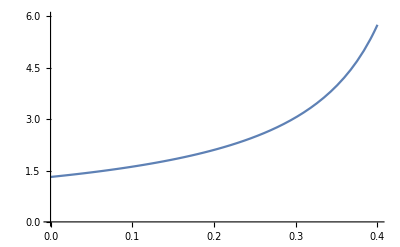

```mathematica
Plot[(Tinf[ϕ]/.params),{ϕ,0,0.4}, PlotRange ->{0,6}]
```

Plot L(T, ϕ) as a function of ϕ, and try to find ϕ* such that L(T, ϕ) is maximal given T

((-1+ⅇ^(t (-a+β (1-ϕ)))) P0 β ϕ)/(-a+β (1-ϕ))

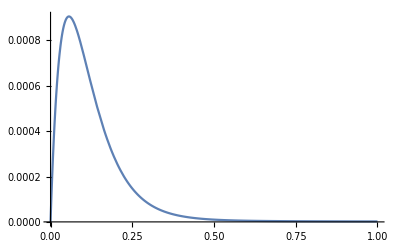

```mathematica
l[t_,ϕ_]= ( β P0 ϕ / ((1-ϕ) β - a) ) (Exp[((1-ϕ)β-a)t] - 1)
Plot[(l[1,ϕ] /. params),{ϕ,0,1}]
```

```mathematica
f[ϕ_] = l[T,ϕ]
g[ϕ_] = f'[ϕ]
FullSimplify[g[ϕ]]
```

((-1+ⅇ^(T (-a+β (1-ϕ)))) P0 β ϕ)/(-a+β (1-ϕ))

((-1+ⅇ^(T (-a+β (1-ϕ)))) P0 β)/(-a+β (1-ϕ))+((-1+ⅇ^(T (-a+β (1-ϕ)))) P0 β^2 ϕ)/(-a+β (1-ϕ))^2-(ⅇ^(T (-a+β (1-ϕ))) P0 T β^2 ϕ)/(-a+β (1-ϕ))

(ⅇ^(-T (a+β (-1+ϕ))) P0 β (-a+ⅇ^(T (a+β (-1+ϕ))) (a-β)+β+a T β ϕ-T β^2 ϕ+T β^2 ϕ^2))/(a+β (-1+ϕ))^2

Trying to find an analytical solution for g[ϕ] == 0 doesn’t work:

```mathematica
Solve[g[ϕ] == 0,ϕ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[((-1+ⅇ^(T (-a+β (1-ϕ)))) P0 β)/(-a+β (1-ϕ))+((-1+ⅇ^(T (-a+β (1-ϕ)))) P0 β^2 ϕ)/(-a+β (1-ϕ))^2-(ⅇ^(T (-a+β (1-ϕ))) P0 T β^2 ϕ)/(-a+β (1-ϕ))==0,ϕ]

However, we can find a numerical solution:

```mathematica
FindRoot[(g[ϕ] == 0 /. params),{ϕ,0.05}]
```

{ϕ→0.0563418}

For later use, we define the derivative function as a function of t (or T...) and ϕ:

```mathematica
m[t_,ϕ_] = D[l[t,ϕ],ϕ]
```

((-1+ⅇ^(t (-a+β (1-ϕ)))) P0 β)/(-a+β (1-ϕ))+((-1+ⅇ^(t (-a+β (1-ϕ)))) P0 β^2 ϕ)/(-a+β (1-ϕ))^2-(ⅇ^(t (-a+β (1-ϕ))) P0 t β^2 ϕ)/(-a+β (1-ϕ))

Plot T(ϕ) together with the numerical solution ϕ* given T

To plot the optimal value ϕ* as a function of T:

```mathematica
j[t_] := FindRoot[(m[t,ϕ] == 0 /. params),{ϕ,0.05}];
j[1]
```

{ϕ→0.0563418}

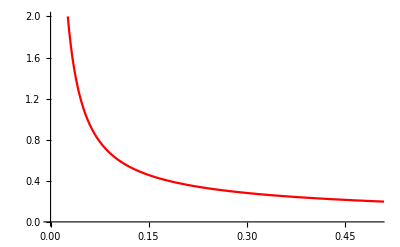

```mathematica
plotdata = Table[{ϕ/.j[t],t}, {t, 0.1, 2, 0.01}];
ListPlot[plotdata, Joined->True, PlotRange-> {{0,0.5},{0,2}}, PlotStyle -> Red]
```

Combine with T(ϕ) to find intersection:

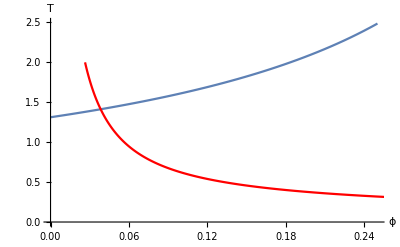

```mathematica
plt1 = Plot[(Tinf[ϕ]/.params),{ϕ,0,0.25}, PlotRange -> {0,2.5}, AxesLabel->{ϕ,T}];
plt2 = ListPlot[plotdata, Joined->True, PlotRange->{{0,0.25},{0,2.5}}, PlotStyle -> {Red}];
Show[plt1, plt2]
```

The ESS is determined by the intersection of these two functions, which we can find for varying values of P0

Redefine functions Tinf and m to depend on P0:

```mathematica
sol = Assuming[{P0>0, ϕ<1-β/a, β>a, a>0}, Simplify[Solve[J[T,ϕ,P0]==1,T, Reals]]]
Tinf[ϕ_,P0_] = T/.sol[[1]]
```

{{T→Log[(P0 β)/(-a+β (1+P0-ϕ))]/(a+β (-1+ϕ))}}

Log[(P0 β)/(-a+β (1+P0-ϕ))]/(a+β (-1+ϕ))

```mathematica
m[t_,ϕ_, P0_] = D[l[t,ϕ],ϕ]
```

((-1+ⅇ^(t (-a+β (1-ϕ)))) P0 β)/(-a+β (1-ϕ))+((-1+ⅇ^(t (-a+β (1-ϕ)))) P0 β^2 ϕ)/(-a+β (1-ϕ))^2-(ⅇ^(t (-a+β (1-ϕ))) P0 t β^2 ϕ)/(-a+β (1-ϕ))

Define the ESS (function of P0) as the intersection between the two curves described above:

```mathematica
ess[P0_] := ϕ/.FindRoot[(m[(Tinf[ϕ, P0] /. params),ϕ, P0]/.params2)==0,{ϕ,0.05}]
```

Test if this indeed yields reasonable ϕ values for default parameters:

```mathematica
ess[P0default]
```

0.0383329

```mathematica
Tinf[ess[P0default], P0default]/.params2
```

1.41266

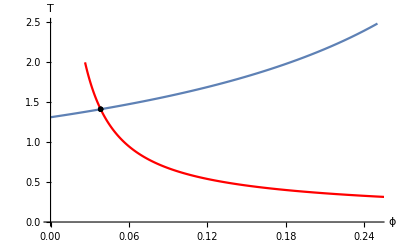

```mathematica
plt3 =ListPlot[{{ess[P0default],Tinf[ess[P0default],P0default]/.params2}},PlotTheme->"Monochrome"];
Show[plt1, plt2, plt3]
```

Plot the ϕ-value of the ESS as a function of the initial phage density P0

Use logarithmic x-axis for P0:

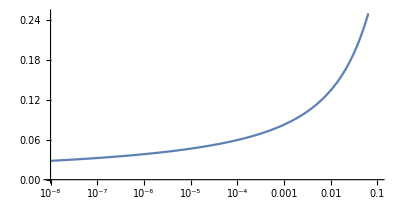

```mathematica
plt4 = LogLinearPlot[ess[lP0], {lP0,10^(-8), 0.1},Ticks->Automatic, AspectRatio->1/2, PlotRange->{0, .25}]
```

Making further simplifying assumptions, we can get an analytical expression for ϕ at ESS

Getting an analytical expression for ϕ* was impossible because we could not solve the root of m[t,ϕ,P0] exactly. However, we can use knowledge of the parameter values to get a pretty good approximation of m (see supporting text S3):

```mathematica
mapprox[t_,ϕ_,P0_] = β P0 Exp[(β(1-ϕ)-a) t]/(β(1-ϕ)-a)((β-a)/(β(1-ϕ)-a) - β t ϕ)
```

(ⅇ^(t (-a+β (1-ϕ))) P0 β ((-a+β)/(-a+β (1-ϕ))-t β ϕ))/(-a+β (1-ϕ))

And by noting that the exponential part is always positive, solving mapprox = 0 reduces to solving msolve = 0 with

```mathematica
msolve[t_,ϕ_,P0_] = (β-a)/(β(1-ϕ)-a) - β  t ϕ
```

(-a+β)/(-a+β (1-ϕ))-t β ϕ

```mathematica
phisolve =FullSimplify[Solve[msolve[t,ϕ,P0]==0, ϕ]]
```

{{ϕ→-(a-β+(√(a-β) √(4+a t-t β))/(√t))/(2 β)},{ϕ→-(a-β-(√(a-β) √(4+a t-t β))/(√t))/(2 β)}}

And by some more algebra (see paper notes), we can derive:

(1-a/β)/Log[PT/P0]

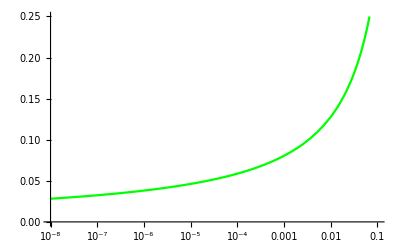

```mathematica
ϕapprox[P0_]= (1 - a/β)/Log[PT/P0]
plt5 =LogLinearPlot[(ϕapprox[P0]/.Append[params2, PT -> 0.5]),{P0,10^(-8),0.1}, PlotRange->{0,0.25}, PlotStyle->{Green}]
```

This approximation is actually really good:

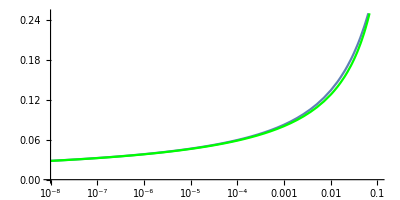

```mathematica
Show[plt4,plt5]
```

However, when making this approximation we ignored that P(T) also depends on ϕ:

```mathematica
PTinf[ϕ_,P0_]=FullSimplify[P0 Exp[((1-ϕ)β-a)Tinf[ϕ,P0]]]
```

1+P0-a/β-ϕ

Next, we substitute this into ϕapprox:
ϕ = (1 - a/β) / Log( (1 - ϕ - a/β) / P0  + 1).
We can try to solve for ϕ:

```mathematica
Solve[ϕ==(ϕapprox[P0]/.PT -> PTinf[ϕ,P0]),ϕ]
```

$Aborted

... but that doesn’t work because ϕ now appears in and out a logarithm. We know that ϕ* is quite small (0<ϕ*<0.1). We can therefore linearly approximate the RHS around ϕ = 0 to get an equation that is linear in ϕ:

```mathematica
ϕRHS[ϕ_,P0_] = (1 - a/β) / Log[(1-ϕ-a/β) /P0 + 1]
Series[ϕRHS[ϕ,P0],{ϕ,0,1}]
ϕRHSlinapprox[ϕ_,P0_] = Normal[%]
```

(1-a/β)/Log[1+(1-a/β-ϕ)/P0]

(1-a/β)/Log[1+1/P0-a/(P0 β)]+((a-β) ϕ)/((a-β-P0 β) Log[1+1/P0-a/(P0 β)]^2)+O[ϕ]^2

((a-β) ϕ)/((a-β-P0 β) Log[1+1/P0-a/(P0 β)]^2)+(1-a/β)/Log[1+1/P0-a/(P0 β)]

Then we can solve ϕ from this linear equation:

```mathematica
sol3 = FullSimplify[Solve[ϕ==ϕRHSlinapprox[ϕ,P0],ϕ]]
```

{{ϕ→((-a+β) (-a+β+P0 β) Log[(-a+β+P0 β)/(P0 β)])/(β (a-β+(-a+β+P0 β) Log[(-a+β+P0 β)/(P0 β)]^2))}}

```mathematica
ϕlinapprox[P0_] =( (β-a)(β-a+β P0) Log[(β-a+β P0)/(β P0)] ) / ( β ( a - β+ (β - a + β P0)(Log[(β -a+β P0)/(β P0)])^2 ) )
```

((-a+β) (-a+β+P0 β) Log[(-a+β+P0 β)/(P0 β)])/(β (a-β+(-a+β+P0 β) Log[(-a+β+P0 β)/(P0 β)]^2))

Compare this new approximation to the full version (plt4) and the previous approximation (plt5)

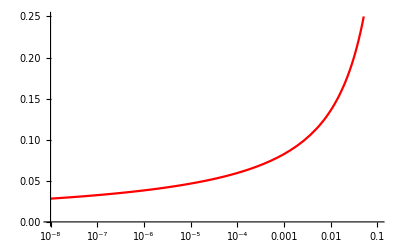

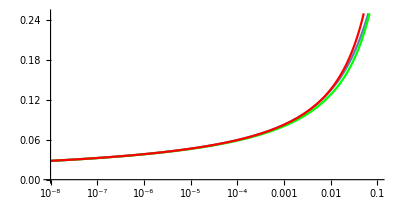

```mathematica
plt6 =LogLinearPlot[(ϕlinapprox[P0]/.params2),{P0,10^(-8),0.1}, PlotRange->{0,0.25}, PlotStyle->{Red}]
Show[plt4,plt5,plt6]
```

This last plot shows that the approximation is still good, especially for small values of P0.